```mathematica
ang2vec[a_]:={Sin[a 2Pi],Cos[a 2 Pi]};
(*component[r_,a_]:= With[{x=r-ang2vec[a]},Max[ang2vec[a].Transpose[x],1.5ang2vec[a-1/4].Transpose[x] - Sqrt[3/4],1.5ang2vec[a+1/4].Transpose[x]-Sqrt[3/4],ang2vec[a+1/2].Transpose[x]] ] *)

component[r_,a_]:=With[{x=r-ang2vec[a]},Max[(ang2vec[a].x) ,-(2-√3-2 ) (ang2vec[a-1/4].x) -1,-(2-√3-2 ) (ang2vec[a+1/4].x)-1, ang2vec[a+1/2].x ]]

(*component[r_,a_]:=Piecewise[{{With[{x=r-ang2vec[a]},Max[(ang2vec[a].x) ,-(2-√3-2 ) (ang2vec[a-1/4].x) -1,-(2-√3-2 ) (ang2vec[a+1/4].x)-1, ang2vec[a+1/2].x ]], r ≠ {0,0}}}, 2/3]*) (*Uncomment for the abstain version of ranking loss *)

exL[{x_, y_}, {p1_, p2_, p3_}] := p1 component[{x,y},0] + p2 component[{x,y},1/3] + p3 component[{x,y},2/3]
Plot3D[component[{x,y},0]+component[{x,y},1/3]+ component[{x,y},2/3],{x,-2,2},{y,-2,2}]
Manipulate[{Plot3D[exL[{x,y}, {p1, p2, 1-p1-p2}], {x,-2,2}, {y,-2,2}](*, Minimize[exL[{x,y}, {p1, p2, 1-p1-p2}], {x,y}]*)}, {p1,0,1}, {p2,0,1}]
```

-Graphics3D-

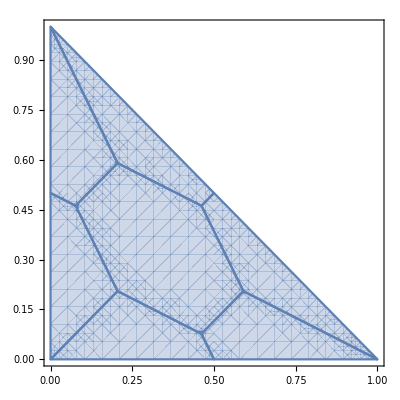

```mathematica
reportset := {{-1,0}, {-1/2, Sqrt[3/4]}, {1/2, Sqrt[3/4]}, {1,0}, {1/2, -Sqrt[3/4]}, {-1/2, -Sqrt[3/4]}, {0,0}}
Losses[{p1_, p2_}] := MapIndexed[exL[#1, {p1, p2 , 1-p1-p2}] &, reportset]
BayesRisk[{p1_, p2_}] :=  Min[Losses[{p1, p2}]]
BR[{p1_,p2_}] :=Simplify[BayesRisk[{p1, p2}], p1≥ 0&& p2 ≥ 0 && p1 + p2 ≤ 1 ]

cell[{r1_, r2_}] := Reduce[exL[{r1, r2}, {p1, p2, 1-p1-p2}]==  BR[{p1, p2}] && p1 ≥ 0 && p2 ≥ 0 && p1 + p2 ≤ 1, { p2}]
Show[MapIndexed[RegionPlot[Evaluate@cell[#1], {p1, 0,1}, {p2, 0, 1}] &, reportset]]
(*Here's our sanity check that the simplex is what we want *)
```